### Integrate ∫_-1^1 (√(1-x^2))/(1+x^2)dx

We have two “different” versions of the function which agree on the upper half plane. For f_2 the Laurent series about z=0 converges for 1 < |z|<∞
	f_2=…+(23 ⅈ)/(16 z^7)-(11 ⅈ)/(8 z^5)+(3 ⅈ)/(2 z^3)-ⅈ/z+0

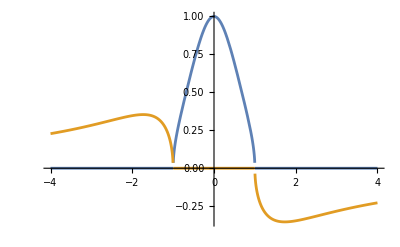

```mathematica
Plot[ {Re[f2[x]],Im[f2[x]]},{x,-4,4}]
```

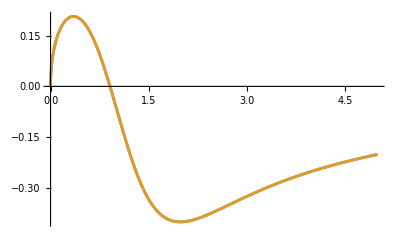

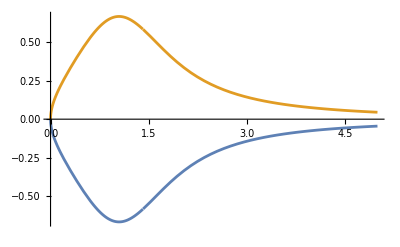

```mathematica
Plot[ {
Re[f2[1+I y]],
Re[f2[-1+I y]]
},{y,0, 5}]
Plot[ {
Im[f2[1+I y]],
Im[f2[-1+I y]]
},{y,0, 5}]
```

```mathematica
g[u_]=Normal[Series[f2[1/u],{u,0,10}]]
g[1/z]
```

-ⅈ u+(3 ⅈ u^3)/2-(11 ⅈ u^5)/8+(23 ⅈ u^7)/16-(179 ⅈ u^9)/128

-(179 ⅈ)/(128 z^9)+(23 ⅈ)/(16 z^7)-(11 ⅈ)/(8 z^5)+(3 ⅈ)/(2 z^3)-ⅈ/z

```mathematica
f1[z_]:=(√(1-z^2))/(1+z^2);f2[z_]:=-(ⅈ √(z-1)√(z+1))/(1+z^2)
TabView[{
"f1"->ComplexPlot3D[f1[z],{z,2},AxesLabel->{"re","im","abs"},
PlotLegends->Automatic],
"f2"->ComplexPlot3D[f2[z],{z,2},AxesLabel->{"re","im","abs"},
PlotLegends->Automatic]
}]
```

12

# ______________ ______________

### Big semicircle outer contour

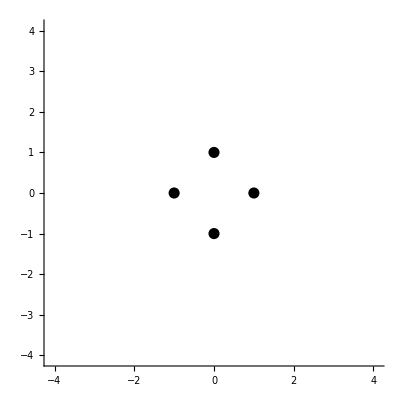

### Tall rectangle contour

-Graphics-

### Big circle outer contour

-Graphics-